```mathematica
boat1=ImplicitRegion[-14≤x≤14&&-(x/3+1.5)^3+Abs[(((z)/13)^4)]≤y≤20&&-28≤z≤28,{x,y,z}];
boat2=ImplicitRegion[-14≤x≤14&&(x/3-1.5)^3+Abs[(((z)/13)^4)]≤y≤20&&-28≤z≤28,{x,y,z}];
boat=RegionIntersection[boat1,boat2]
water = ImplicitRegion[y<Tan[θ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}]
under=RegionIntersection[boat,water]
Manipulate[RegionPlot3D[{under/.{d->dd,θ->θθ},water/.{d->dd,θ->θθ},boat},AspectRatio->Automatic, PlotTheme->"Scientific",AxesLabel->{x,y,z}],{{dd,1,"Waterline draft"},-5,20,Appearance->"Labeled"},{{θθ,1,"Waterline Angle"},0,180,Appearance->"Labeled"}]
```

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/28561≤y≤20&&-0.037037 (4.5+x)^3+z^4/28561≤y≤20,{x,y,z}]

ImplicitRegion[y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/28561≤y≤20&&-0.037037 (4.5+x)^3+z^4/28561≤y≤20&&y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

```mathematica
Submerged[θθ_]:=Module[{},
mass= 402.93+1000;
com = {0,18.217,0};
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->θθ}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft,θ->θθ}];
buoyancy = mass*980*{-Sin[θθ Degree],Cos[θθ Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

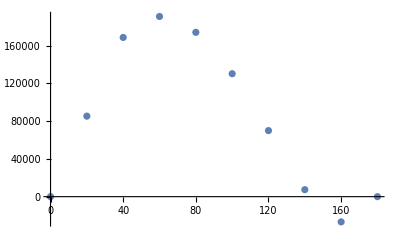

```mathematica
ListPlot[Table[{theta,Submerged[theta]},{theta,{0,20,40,60,80,100,120,140,160,180}}]]
```